Alejandra Ortiz

## Modelo de Boids (dominio finito)

### Funciones necesarias

#### Función para generar a los individuos

```mathematica
AddBoid[dominio_,velocidad_]:= Module[{x,y,theta,color},
x = Random[]*dominio; y = Random[]*dominio;
theta = Random[] * 2Pi;color = RGBColor[Random[],Random[],Random[]];
{{x,y},{velocidad*Cos[theta],velocidad*Sin[theta]},color}  ];
```

#### Función para visualizar a los individuos

```mathematica
ShowBoid[{{x_,y_},{vx_,vy_},color_}] := Module[{rt,theta,alturatriangulo,anchotriangulo},alturatriangulo=15;anchotriangulo =10 ;theta = If[vx==0,0,ArcTan[vy/vx]];If[vx<0,theta+=Pi];rt= RotationTransform[theta,{x,y}];
{color,Polygon[{rt@{x-alturatriangulo/2,y+anchotriangulo/2},rt@{x-alturatriangulo/2,y-anchotriangulo/2},rt@{x+alturatriangulo/2,y}}]} ];
```

#### Función para visualizar el dominio con los individuos

```mathematica
Render[listaindividuos_,dominio_] := Module[{ListaGraficos},
ListaGraficos = ShowBoid/@listaindividuos;
Graphics[{EdgeForm[Directive[Thick,White]],{White,Rectangle[{0,0},{dominio,dominio}]},EdgeForm[Directive[AbsoluteThickness[0.3],Black]],ListaGraficos},PlotRange->{{0,dominio},{0,dominio}},ImageSize->1.13{300,300}, ImagePadding -> None]]
```

#### Funciones de Fronteras, Ángulo y distancia

```mathematica
OffScreenQ[{{x_,y_},___},dominio_] :=OffScreenQ[{{x,y},___},dominio,offscreenOffset=30];
OffScreenQ[{{x_,y_},___},dominio_,offset_] :=x+offset<0||x-offset>dominio||y+offset<0||y-offset>dominio;
```

```mathematica
AngleBetween[{loc1_,vector1_, ___},{loc2_, ___}] := Module[{vector2},vector2 = loc2-loc1; 
If[vector2=={0,0}||vector1=={0,0},0,VectorAngle[vector1,vector2]]];
DistanceBetweenSq[loc1_,loc2_] := Total@((loc2-loc1)^2);
```

#### Función de actualización

```mathematica
(*Checa todos con todos y esta algo pesada*)
UnPaso[{loc_,vel_,other___},listaindividuos_,dominio_,RangoDeteccion_,RangoCollision_,CenterPower_,FlockingPower_,CollisionPower_,VelocidadMaxima_,Rebote_:True] :=Module[{cercania,colision,detectada,avgVel={0,0},avoidVel={0,0},newVel=vel,newLoc},DeteccionAngulo =2Pi(*50/360*2Piangulo de detección*);
cercania = Select[listaindividuos,(DistanceBetweenSq[loc,#⟦1⟧] < RangoDeteccion^2&)];
colision = Select[listaindividuos,(DistanceBetweenSq[loc,#⟦1⟧] < RangoCollision^2&)];
If[!Length@cercania == 0,detectada = Select[cercania,(AngleBetween[{loc,vel},#]<DeteccionAngulo&)];
If[Length@detectada > 0,avgVel = Mean[#⟦2⟧&/@detectada];newVel +=FlockingPower*avgVel; ];newVel += CenterPower*Normalize[Mean[#⟦1⟧&/@cercania]-loc];];
If[Length@colision > 0, avoidVel =Plus@@(-( #⟦1⟧-loc)&/@colision);
newVel += CollisionPower* avoidVel;];
If[Norm[newVel] > VelocidadMaxima, newVel = VelocidadMaxima * Normalize[newVel]; ]; newLoc=loc+newVel;
If[Rebote,{newLoc,newVel}=(If[#⟦1⟧ < 0, -#, If [#⟦1⟧ > dominio, {2 dominio - #⟦1⟧, -#⟦2⟧},# ]
     ] &) /@ (Transpose@{newLoc,newVel}) // Transpose;{newLoc,newVel,other}];
{loc+newVel,newVel,other} ]
```

#### Función de actualización

```mathematica
Paso[a_]:=Module[{VelocidadMaxima,RangoDeteccion,FlockingPower,CenterPower,RangoCollision,CollisionPower},VelocidadMaxima=8;RangoDeteccion=50;FlockingPower=.1;CenterPower=.1;RangoCollision=50;CollisionPower=.1;
UnPaso[#,listaindividuos,dominio,RangoDeteccion,RangoCollision,CenterPower,FlockingPower,CollisionPower,VelocidadMaxima]&/@a]
```

#### Función Boid

```mathematica
dominio=500;velocidad=3;numeroind=30;listaindividuos=Table[AddBoid[dominio,velocidad],{numeroind}];
```

```mathematica
Boid[numeropasos_,dominio_,numeroind_,velocidad_]:=Module[{lista,listaindividuos},
listaindividuos=Table[AddBoid[dominio,velocidad],{numeroind}];lista=NestList[Paso,listaindividuos,numeropasos];
ListAnimate[Table[Render[lista⟦i⟧,dominio],{i,1,Length[lista]}],DefaultDuration->20,ControlPlacement->Bottom]]
```

```mathematica
Boid[500(*tiempo*),500(*tamaño del dominio*),30(*numero individuos*),3(*velocidad maxima*)]
```

## Otra forma de realizarlo tomando en cuenta solo los cercanos con un dominio Toroidal

Checamos los puntos más cercanos en un radio r:

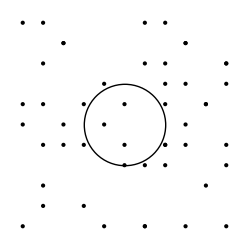

### Funciones de inicialización

```mathematica
Inicializacion[dominio_,numero_]:= Module[{x,y,theta,color},
x = RandomReal[dominio,{numero}]; y = RandomReal[dominio,{numero}];
theta = RandomReal[2Pi,{numero}] ;color =RandomColor[numero];Table[{{x[[i]],y[[i]]},theta[[i]],color[[i]]},{i,1,numero}]]
```

```mathematica
ini=Inicializacion[500,50]
```

{{{296.858,105.476},4.86541,RGBColor[0.7341687168262017, 0.7458899824329395, 0.3816787960020369]},{{91.3118,25.3613},5.53834,RGBColor[0.18071749591735653, 0.9499754915864984, 0.1038438034079483]},{{99.6973,450.919},3.747,RGBColor[0.40024861215186736, 0.6118089584921815, 0.7802324452070439]},{{138.923,177.49},2.15341,RGBColor[0.061317137625555684, 0.28875899077174605, 0.02183015288012835]},{{142.27,318.725},1.07516,RGBColor[0.8555286273062126, 0.25121974891663346, 0.5049315421472971]},{{415.178,297.491},1.06672,RGBColor[0.5455939793797366, 0.3475778128997844, 0.7251155502065447]},{{55.2676,32.8809},4.65497,RGBColor[0.2955394459001248, 0.016071848428258928, 0.9373438195732224]},{{290.715,466.699},4.077,RGBColor[0.07133012836742547, 0.5557001960655057, 0.3471896685569964]},{{480.775,242.554},5.14237,RGBColor[0.2906856194457945, 0.21202764809602948, 0.5718748592703389]},{{127.133,87.869},1.83093,RGBColor[0.45076479501107847, 0.40888572875079654, 0.9286447441958312]},{{75.372,212.74},1.80444,RGBColor[0.41491598883359093, 0.1308145436832251, 0.7333999579625159]},{{120.156,193.534},1.2441,RGBColor[0.38906346138700854, 0.18742739090565164, 0.17403912284887713]},{{303.038,473.033},4.86208,RGBColor[0.09989559621484867, 0.7815231594132224, 0.18776786193884232]},{{372.738,9.18027},0.925989,RGBColor[0.28009255820188295, 0.8436479393876515, 0.28686525310279354]},{{144.559,32.6951},6.05733,RGBColor[0.2575362236036778, 0.08388764951994387, 0.7926137801311779]},{{70.552,153.511},3.54909,RGBColor[0.32802792996129293, 0.8773929165420673, 0.9147036035614404]},{{322.06,459.095},5.2682,RGBColor[0.7566859846639524, 0.6399645248700025, 0.7324391529054404]},{{270.422,486.9},5.30894,RGBColor[0.781527470136099, 0.19542505137895416, 0.2283113876168965]},{{402.842,135.172},0.519767,RGBColor[0.5824271527631335, 0.36230858100159846, 0.30067994627588956]},{{318.382,98.4504},0.302432,RGBColor[0.9146397777427286, 0.820227356195441, 0.6894830272578365]},{{131.444,63.4742},5.13549,RGBColor[0.692581189190028, 0.8743836489009376, 0.32345213720005006]},{{184.998,210.858},3.86748,RGBColor[0.8622057652757578, 0.5904170411516076, 0.7296458705372495]},{{339.988,382.656},1.19765,RGBColor[0.853268235249895, 0.06700091494390747, 0.6965146693241844]},{{364.263,397.031},5.91508,RGBColor[0.3014002648705494, 0.026203881547457453, 0.3184396695635967]},{{439.813,470.025},5.98478,RGBColor[0.22327378392644026, 0.1244341222696399, 0.29271095087038645]},{{92.2029,12.8176},4.92352,RGBColor[0.9289735235465015, 0.4068369722340217, 0.8684113997772738]},{{392.874,180.058},3.05732,RGBColor[0.46055497560327496, 0.5116658963127059, 0.38055588840290033]},{{309.433,265.121},5.60899,RGBColor[0.20244398727894852, 0.21635554960984815, 0.13186826205849678]},{{316.022,307.302},3.35858,RGBColor[0.42773908853770104, 0.38117808527486075, 0.4803522858810336]},{{469.077,14.2214},4.1656,RGBColor[0.5724377498227364, 0.1917415424699076, 0.7181014473436746]},{{477.444,235.637},4.87169,RGBColor[0.9740775599127918, 0.9365776459634163, 0.12387869732288004]},{{417.455,81.0158},2.58348,RGBColor[0.28560017317461317, 0.8854132096447289, 0.25611710499102247]},{{492.626,8.06275},5.94033,RGBColor[0.3388915132615873, 0.5372801734783652, 0.8946264390151144]},{{442.465,366.005},1.23004,RGBColor[0.8572755685946203, 0.6776400485021898, 0.9976484014001239]},{{488.042,350.034},0.120197,RGBColor[0.38695162970967667, 0.5140935999813263, 0.03833555503729902]},{{192.922,202.286},0.829906,RGBColor[0.13660660226284982, 0.9570555149175646, 0.48565798590878906]},{{308.271,0.865738},1.01908,RGBColor[0.018012640011620062, 0.5564876003731012, 0.31794267402919507]},{{158.335,470.082},4.92913,RGBColor[0.28159527183155664, 0.337397760920094, 0.19755467293516737]},{{470.102,236.308},3.24857,RGBColor[0.8058603168572855, 0.10194798819504935, 0.7620914278941269]},{{68.9242,366.571},0.343139,RGBColor[0.806930502949154, 0.9908522460709062, 0.49417550589545023]},{{55.4146,403.985},1.61132,RGBColor[0.266929454486202, 0.1633522541119814, 0.9639306025433809]},{{427.707,388.636},5.28293,RGBColor[0.4331553800061674, 0.7587409891755628, 0.18032751143784043]},{{380.509,426.012},0.196138,RGBColor[0.4127699869724022, 0.21016249865613879, 0.5635327841418276]},{{312.991,243.571},6.07249,RGBColor[0.277988814312234, 0.647441078211177, 0.8797660385525807]},{{54.5665,55.8787},3.45228,RGBColor[0.16929120323862934, 0.9047867245559982, 0.5234674756546149]},{{86.9877,72.4004},4.9859,RGBColor[0.03003924317605411, 0.903311868690809, 0.6257800892304419]},{{485.179,203.753},0.859641,RGBColor[0.7406443525417565, 0.8104613391322879, 0.41110520355872704]},{{173.195,28.6663},5.57635,RGBColor[0.037660575369635296, 0.2662492991797669, 0.2602020538703891]},{{317.191,232.269},0.955422,RGBColor[0.7576500989162906, 0.7412069610759122, 0.09227904361363448]},{{170.057,379.811},0.301144,RGBColor[0.18394955105018784, 0.4540764300417244, 0.5058991362422713]}}

```mathematica
ShowBoid[{{x1_,y1_},th_,color_}] := Module[{alturatriangulo,anchotriangulo},alturatriangulo=15;anchotriangulo =10 ;x=Mod[x1,500];y=Mod[y1,500];{color,GeometricTransformation[Polygon[{{x-alturatriangulo/2,y+anchotriangulo/2},{x-alturatriangulo/2,y-anchotriangulo/2},{x+alturatriangulo/2,y}}],RotationTransform[th,{x,y}]]} ];
```

```mathematica
Render[listaindividuos_,dominio_] := Module[{ListaGraficos},
ListaGraficos = ShowBoid/@listaindividuos;
Graphics[{EdgeForm[Directive[Thick,White]],{White,Rectangle[{0,0},{dominio,dominio}]},EdgeForm[Directive[AbsoluteThickness[0.3],Black]],ListaGraficos},PlotRange->{{-10,dominio+10},{-10,dominio+10}},ImageSize->1.13{300,300}, ImagePadding -> None]]
```

```mathematica
Paso[ini_]:=Module[{criticalRadius,noncriticalRadius,choque,ini2,angle,pos,centros},centros=ini⟦;;,1⟧;
criticalRadius=10;
noncriticalRadius=30;
ini2=ini;
choque=Table[Pick[DeleteCases[centros,centros[[i]]],UnitStep[criticalRadius^2-Total[(Transpose[DeleteCases[centros,centros[[i]]]]-centros[[i]])^2]],1],{i,1,Length[centros]}];
Table[If[Length[choque[[i]]]==1,ini2⟦i,2⟧=-ini2⟦i,2⟧;ini2⟦i,1⟧=ini2⟦i,1⟧+5{Cos[ini2⟦i,2⟧],Sin[ini2⟦i,2⟧]},pos=Position[UnitStep[noncriticalRadius^2-Total[(Transpose[DeleteCases[centros,centros[[i]]]]-centros[[i]])^2]],1];
If[Length[pos]==0,ini2⟦i,1⟧=ini2⟦i,1⟧+5{Cos[ini2⟦i,2⟧],Sin[ini2⟦i,2⟧]},
ini2⟦i,2⟧=VectorAngle[{1,0},{1+Total[Cos[Table[ini2[[pos[[i]],2]],{i,1,Length[pos]}]]][[1]],Total[Sin[Table[ini2[[pos[[i]],2]],{i,1,Length[pos]}]]][[1]]}];
angle=VectorAngle[ini[[i,1]],
Quiet[RegionCentroid[RegionBoundary@BoundingRegion[Table[ini2[[pos[[i]],1]][[1]],{i,1,Length[pos]}],"MinDisk"]]]];
ini2⟦i,1⟧=ini2⟦i,1⟧+5{Cos[angle],Sin[angle]}]],{i,1,Length[choque]}];ini2]
```

### Resultado:

```mathematica
list=NestList[Paso,ini,100];
```

```mathematica
Animate[Render[list[[i]],500],{i,1,100,1},ControlPlacement->Bottom]
```

En este caso los individuos se alinean mas rapido y forman grupos,